```mathematica
GraphAssortativity[RandomGraph[{100, 300}]]
```

-463/6861

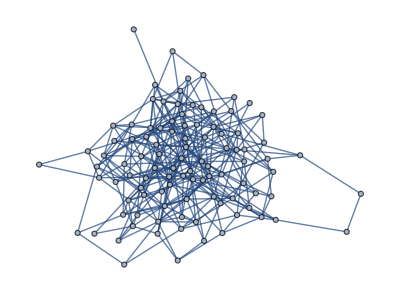

-0.00966932

```mathematica
g=RandomGraph[{100, 300}];Print[Graph[g]]; Print[N[GraphAssortativity[g]]];
```

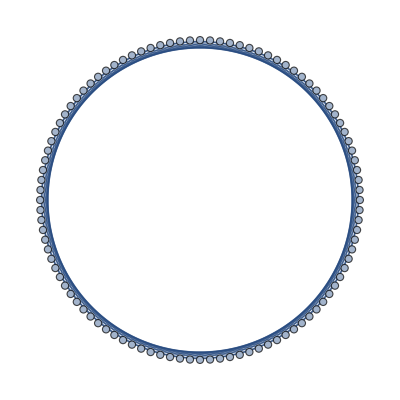

0.

```mathematica
g=CirculantGraph[100, 10];Print[Graph[g]]; Print[N[GraphAssortativity[g]]];
```

```mathematica
n=1000; m=1;
```

```mathematica
kaux={}; cc={}; ncc=0; scc={}; x=0; lncc={}; lvd={}; lscc={}; lgc={}; lmc={}; llcc={}; distt=ConstantArray[0,1000]; distr=ConstantArray[0, 1000]; diamt={}; diamr={}; Do[{kaux={}; v={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Rhodep\\Net_090.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Rhodep\\Net_090.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}]},m];Print[Graph[t]];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

```mathematica
Length[ConnectedComponents[Graph[t]]]
```

25

```mathematica
Graph[t]
```

-Graphics-

```mathematica
VertexCount[%4]
```

960

-Graphics-

```mathematica
t={1<->6,1<->4,1<->3,1<->2,2<->6,2<->4,2<->3,3<->6,3<->4,4<->6,5<->6,5<->4,5<->3,5<->1,0<->0}
```

{1<->6,1<->4,1<->3,1<->2,2<->6,2<->4,2<->3,3<->6,3<->4,4<->6,5<->6,5<->4,5<->3,5<->1,0<->0}

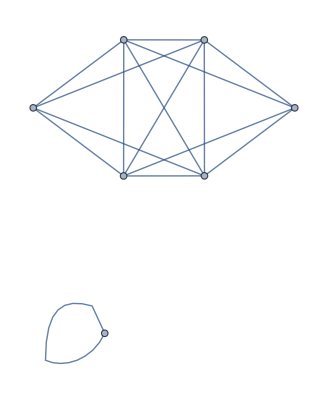

```mathematica
Graph[t]
```

```mathematica
Graph[t]
```

Graph[{1<->6,1<->4,1<->3,1<->2,2<->6,2<->4,2<->3,3<->6,3<->4,4<->6,5<->6,5<->4,5<->3,5<->1,0,0<->0}]

```mathematica
diamt
```

{15}

```mathematica
FindPath[Graph[t],99, 97]
```

{{99,77,83,39,14,79,2,67,53,16,4,47,64,3,97}}

```mathematica
n=7; m=1;
```

```mathematica
kaux={}; cc={}; ncc=0; scc={}; x=0; lncc={}; lvd={}; lscc={}; lgc={}; lmc={}; llcc={}; distt=ConstantArray[0,1000]; distr=ConstantArray[0, 1000]; diamt={}; diamr={}; Do[{kaux={}; v={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Flux100.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Flux100.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}],f=DeleteCases[Flatten[UpperTriangularize[GraphDistanceMatrix[Subgraph[t, First[ConnectedComponents[t]]]]]], 0], Do[{distt[[i]]=distt[[i]]+2*Count[f, i]}, {i, 1, 100}], diamt=Join[diamt, {Max[f]}]},m];
```

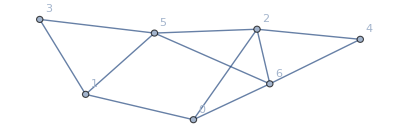

```mathematica
Graph[t, VertexLabels->Automatic]
```

```mathematica
N[MeanClusteringCoefficient[Graph[t]]]
```

0.571429

```mathematica
MeanClusteringCoefficient[Graph[t]]
```

4/7

```mathematica
LocalClusteringCoefficient[Graph[t], 6]
```

1/2